# Animiranje grafov, vektorji in matrike

## Animiranje grafov

### Subsection. naloga:

Narišite graf funkcije y=a sin (k x+n) tako, da boste lahko vrednosti parametrov a, k in n spreminjali v obsegu od -3 do 3. Območje risanja omejite na [-5,5]×[-5,5]. Enoti na x in y osi naj bosta enako veliki.

```mathematica
(* V funkciji Plot uporabite nastavitvi Range->{-5,5} in AspectRatio->Automatic *)
```

```mathematica
Manipulate[
Plot[a Sin[k x+n],{x, -5,5}, AspectRatio->Automatic, PlotRange->{-5, 5}],
{a, -3, 3},
{k, -3, 3},
{n, -3, 3}
]
```

### Subsection. naloga:

Narišite graf premice y=k x+n  in na isti sliki še pravokotnico nanjo, ki gre skozi točko T(x_0,y_0) tako, da boste lahko spreminjali vrednosti parametrov k, n, x_0 in y_0. Na sliki označite z majhnim krogcem, kje leži točka T.
Namig: dva grafa na isti sliki narišete s funkcijo Plot tako, da predpisa podate v seznamu: {f[x], g[x]}.

```mathematica
(* Točko dodate z nastavitvijo Epilog->{PointSize[Large],Point[{{x0,y0}}]}] *)
```

```mathematica
Manipulate[
Plot[{k x+n, -(1/k) x +y0+(1/k )x0}, {x , -5, 5},  AspectRatio->Automatic, PlotRange->{-5, 5}, Epilog->{PointSize[Large],Point[{{x0,y0}}]}],
{k, -3, 3},
{n, -3, 3},
{x0, -3, 3},
{y0, -3, 3}
]
```

### Subsection. naloga:

Definirajte funkcijo  f(x)=(x(x-2))^2/(x^2+1) ter narišite njen graf skupaj s tangento v točki x_0, tako da boste lahko spreminjali vrednosti parametra x_0. Na sliki označite z majhnim krogcem, kje se tangenta dotika grafa funkcije. f(x0)=f’(x0)* x0+n

```mathematica
f[x_]:=(x (x-2)^2)/(x^2+1)
Manipulate[
Plot[{f[x], f'[x0]x+f[x0]-f'[x0] x0}, {x, -5, 5}, AspectRatio->Automatic, PlotRange->{-5, 5}],
{x0, -3, 3}
]
```

### Subsection. naloga:

1. Narišite graf implicitno podane funkcije  |x|^(2/3)+|y|^(2/3)=1  na območju [-1,1]×[-1,1]
2. Prikažite, kako se spreminja graf implicitne krivulje  |x|^p+|y|^p=1  za vrednosti parametra p∈[0,4]  z začetno vrednostjo 2.
3. Pri kateri vrednosti p leži točka (1/3,1/3) na grafu krivulje?

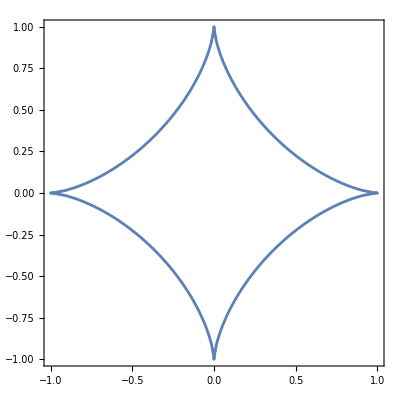

```mathematica
ContourPlot[Abs[x]^(2/3)+Abs[y]^(2/3)==1, {x, -1, 1}, {y, -1, 1}]
```

```mathematica
Manipulate[
ContourPlot[Abs[x]^(p)+Abs[y]^(p)==1, {x, -1, 1}, {y, -1, 1}],
{{p, 2, "Phase Parameter"}, 0, 4}
]
```

```mathematica
p/. Solve[Abs[1/3]^(p)+Abs[1/3]^(p)==1, p]
```

{ConditionalExpression[(2 ⅈ π C[1])/Log[3]+Log[2]/Log[3], C[1]∈ℤ]}

## Vektorji in matrike

### Subsection. naloga:

1. Dana sta vektorja  (v⃗)_1=(1,2,3)  in  (v⃗)_2=(-3,-2,5). Zapiši ju kot dve spremenljivki.
2. Izračunaj njun skalarni produkt.
3. Izračunaj njun vektorski produkt.s
4. Kateri od vektorjev je daljši?
5. Sestavi enačbo ravnine, ki gre skozi točko (1,1,1) in ima normalo v smeri vektorskega produkta.

```mathematica
ClearAll
v1={ 1, 2, 3}
v2={ -3, -2, 5}
v1 . v2
v1×v2
d1:=Norm[v1]
d2:=Norm[v2]
Evaluate[d1<d2]


Simplify[Solve[((v1×v2)/Norm[v1×v2]).{x, y, z}==((v1×v2)/Norm[v1×v2]).{1, 1, 1},{ x,y,z}]/.Rule->Equal]
```

ClearAll

{1,2,3}

{-3,-2,5}

8

{16,-14,4}

True

Solve::svars: Equations may not give solutions for all "solve" variables.

{{3+7 y==8 x+2 z}}

### Subsection. naloga:

Naj bodo a⃗, b⃗ in c⃗ vektorji v R^3. S simboličnim računom dokaži identiteto  a⃗×(b⃗×c⃗)=(a⃗·c⃗)b⃗-(a⃗·b⃗)c⃗

```mathematica
a:={a1, a2, a3}
b:={b1, b2, b3}
c:={c1, c2, c3}
Simplify[a×(b×c)]==Simplify[(a.c) b-(a.b) c]
```

True

### Subsection. naloga:

Dokaži, da za poljubni 2×2 matriki A in B velja enakost  (A B)^-1=B^-1 A^-1.

```mathematica
ClearAll
A:={{a1, a2},{a3, a4}}
B:={{b1, b2},{b3, b4}}
Simplify[Inverse[A .B]==Inverse[B].Inverse[A]]
```

ClearAll

True

```mathematica
ClearAll
```

ClearAll

### Subsection. naloga:

1. Dana je matrika  M=(9 | 2 | -3
3 | 2 | 1
6 | 4 | -1).  Zapiši jo kot spremenljivko.
2. Izračunaj njeno determinanto.
3. Izračunaj njene lastne vrednosti.
4. Izračunaj njene lastne vektorje.
5. Ali je matrika diagonalizabilna?
6. Matriko želimo diagonalizirati. Konstruiraj diagonalno matriko (po diagonali ima lastne vrednosti), prehodno matriko (za stolpce ima lastne vektorje) in inverz prehodne matrike.
7. Preveri, ali velja pogoj za diagonalizabilnost.

```mathematica
ClearAll
M={{9, 2, -3}, {3, 2, 1}, {6, 4, -1}}
M//MatrixForm
Det[M]
Eigenvalues[M]
Eigenvectors[M]
MatrixRank[M]==3
Dia=DiagonalMatrix[Eigenvalues[M]]
Dia//MatrixForm
P=Transpose[Eigenvectors[M]]
P//MatrixForm
Simplify[M==P.Dia.Inverse[P]]
```

ClearAll

{{9,2,-3},{3,2,1},{6,4,-1}}

(9 | 2 | -3
3 | 2 | 1
6 | 4 | -1)

-36

{3 (1+√2),4,3 (1-√2)}

{{-(-6-5 √2)/(6 (1+√2)),-(-2-√2)/(2 (1+√2)),1},{2,7,8},{-(-5+3 √2)/(3 √2 (-1+√2)),-(2-√2)/(2 (-1+√2)),1}}

True

{{3 (1+√2),0,0},{0,4,0},{0,0,3 (1-√2)}}

(3 (1+√2) | 0 | 0
0 | 4 | 0
0 | 0 | 3 (1-√2))

{{-(-6-5 √2)/(6 (1+√2)),2,-(-5+3 √2)/(3 √2 (-1+√2))},{-(-2-√2)/(2 (1+√2)),7,-(2-√2)/(2 (-1+√2))},{1,8,1}}

(-(-6-5 √2)/(6 (1+√2)) | 2 | -(-5+3 √2)/(3 √2 (-1+√2))
-(-2-√2)/(2 (1+√2)) | 7 | -(2-√2)/(2 (-1+√2))
1 | 8 | 1)

True